### • Import Functions

```mathematica
SetDirectory["C:\\Users\\Sean\\Google Drive\\financialdata\\SP500 Dates"];
(*SetDirectory["C:\\Users\\shuver\\Google Drive\\financialdata\\SP500 Dates"];*)
(*SetDirectory["/home/shuver/Mathematica/data"]*)

SP500=Import["SP500.csv"];
SP500[[1]]
SP500=Drop[SP500,1];

Length[SP500]
```

{Date,SPY Close,SPY Open,SPY High,SPY Low,Nikkei Close,DAX Close,DAX Open,DAX High,DAX Low,Day Val,FTSE Close,USDI Close,FTSE Open,FTSE High,FTSE Low,Nik Open,Nik High,Nik Low,SPY Vol/20,Date Val,SPY Close,CloseDiff %,5-STD Close,10 STD,20 STD,,,,,,}

3210

### • Get Data

```mathematica
(* best list so far {2,3,4,5,6,8,9,11,13,16,17,18,21,22}  *)
randomizedInputList={2,3,4,5,6,8,9,11,13,16,17,18,21,22} ;
scale=.5;
getTrainingData[input_,startDay_,numDays_,K_]:=Module[{},
(*uTrain=ParallelTable[input[[i,j]],{i,startDay,startDay+numDays},{j,2,K+1}];*)
uTrain=Table[N[scale*input[[i,j]]],{i,startDay,startDay+numDays},{j,randomizedInputList}];
trainOutputs=Table[Sign[input[[i,2]]],{i,startDay+1,startDay+numDays+1}];
For[i=1,i<Length[trainOutputs],i++,
If[trainOutputs[[i]]==0,trainOutputs[[i]]=-1];
];
Return[{uTrain,trainOutputs}];
]

getTestData[input_,startDay_,numDays_,K_]:=Module[{},
(*U=ParallelTable[input[[i,j]],{i,startDay,startDay+numDays},{j,2,K+1}];*)
U=Table[N[scale*input[[i,j]]],{i,startDay,startDay+numDays},{j,randomizedInputList}];
runOutputs=Table[Sign[input[[i,2]]],{i,startDay+1,startDay+numDays+1}];
StartTestDate=input[[startDay+1,1]];
EndTestDate=input[[startDay+numDays+1,1]];
(*
Print["Start of Testing Data: ",StartTestDate];
Print["End of Testing Data: ",EndTestDate];
*)
Return[{U,runOutputs}];
]
getDayOfWeek[date_]:=Module[{},
Quiet[If[DayName[date]==Monday,Return[.01]]];
Quiet[If[DayName[date]==Tuesday,Return[.02]]];
Quiet[If[DayName[date]==Wednesday,Return[.03]]];
Quiet[If[DayName[date]==Thursday,Return[.04]]];
Quiet[If[DayName[date]==Friday,Return[.05]]];
]
getDateValue[date_]:=Module[{dateVal},
dateVal=Quiet[DateList[date]];
If[dateVal[[2]]== 1 ||dateVal[[2]]== 3 ||dateVal[[2]]== 5 ||dateVal[[2]]== 7 ||dateVal[[2]]== 8 ||dateVal[[2]]==10 || dateVal[[2]]==12, Return[N[dateVal[[3]]/31/20]]];
If[dateVal[[2]]==4||dateVal[[2]]==6||dateVal[[2]]==9||dateVal[[2]]==11, Return[N[dateVal[[3]]/30/20]]];
If[dateVal[[2]]==2,Return[N[dateVal[[3]]/28/20]]];
]
getRandomInput[K_]:=Module[{}, (* Gets random set of input from data *)
inputList={2,3,4,5};
inputList=Append[inputList,RandomSample[Range[18]+5,K-4]];
Return[Sort[Flatten[inputList]]]; (* Returns randomized input in sorted fashion *)
]
```

### • Support Vector Machine Definitions

```mathematica
svmSolver[x_,y_,kernalType_,c_,γ_]:=Module[{m,n,L,constraints,vars,bdata,sol,Kernal,b},
n=Length[x];
m=Length[x[[1]]];
(* kernalType {1-> Gaussian, 2-> Linear, 3-> Polynomial, 4-> Sigmoid} *)
If[kernalType==1,K[u_,v_]:=Exp[-γ(u-v).(u-v)]];
If[kernalType==2,K[u_,v_]:=u.v];
If[kernalType==3,K[u_,v_]:=(γ*u.v+r)^3];
If[kernalType==4,K[u_,v_]:=γ*u.v+r];
(* Make Kernal Matrix *)
Kernal=(Table[N[K[x[[i]],x[[j]]]],{i,1,n},{j,1,n}]+(1/c)IdentityMatrix[n]);
(* Lagrangian to be maximized *)
L=∑_(i=1)^n Subscript[α, i]-1/2∑_(i=1)^n ∑_(j=1)^n y[[i]]y[[j]]Kernal[[i,j]](Subscript[α, i]*Subscript[α, j]);
constraints=Apply[And,Join[Table[Subscript[α, i]≥0,{i,1,n}],{∑_(i=1)^n y[[i]] Subscript[α, i]==0}]];
vars=Table[Subscript[α, i],{i,1,n}];
sol=NMaximize[{L,constraints},vars,Method->"DifferentialEvolution"][[2]];
sol=Chop[sol,10^-3];
bdata=Table[((1-Subscript[α, j]/c)/y[[j]]-∑_(i=1)^n y[[i]] Subscript[α, i] K[x[[i]],x[[j]]])/.sol,{j,1,n}];
b=Mean[bdata];
Return[{sol,b}];
];
svmClassify[x_,y_,testData_,testSol_,αSol_,bSol_]:=Module[{vars,n,results,svmClassifier,hitVal},
n=Length[x];
vars=Table[Subscript[α, i],{i,1,n}];
svmClassifier[w_]:=((∑_(i=1)^n y[[i]] Subscript[α, i] K[x[[i]],w])+bSol)/.αSol;
results=Table[Sign[svmClassifier[testData[[i]]]],{i,1,Length[testData]}];
hitVal=N[Count[results-testSol,0]/Length[results]];
Return[hitVal];
];
svmRun[input_,start_,trainDays_,testDays_,dataDim_,kernalType_,c_,γ_]:=Module[{alpha,bval,trainIN,trainOUT,testIN,testOUT,result},
{trainIN,trainOUT}=getTrainingData[input,start,trainDays,dataDim];
{testIN,testOUT}=getTestData[input,start+trainDays,testDays,dataDim];
{alpha,bval}=svmSolver[trainIN,trainOUT,kernalType,c,γ];
result=svmClassify[trainIN,trainOUT,testIN,testOUT,alpha,bval];
Return[result];
];
svmLongRunsvmRun[input_,start_,trainDays_,testDays_,dataDim_,kernalType_,c_,γ_]:=Module[{iMax,result},
iMax=80;
result=ParallelTable[svmRun[input,start+i*10,trainDays,testDays,dataDim,kernalType,c,γ],{i,0,iMax}];
Print[iMax," 10 trading day periods. "];
Print["Average prediction success: ",Mean[result]];
Return[result];
];
svmLongGDSearch[input_,start_,trainDays_,testDays_,dataDim_,kernalType_]:=Module[{iMax,result},
iMax=5;
result=ParallelTable[{svmRun[input,start+l*10,trainDays,testDays,dataDim,kernalType,j,k],l,j,k},{l,0,iMax},{j,25,75,25},{k,25,100,25}];

Print[iMax," 10 trading day periods. "];
Return[result];
];
```

```mathematica
trainDays=80;
testDays=10;
startDay=2600;
dataDim=14;
trainData=getTrainingData[SP500,startDay,trainDays,dataDim];
testData=getTestData[SP500,startDay+trainDays,testDays,dataDim];
```

```mathematica
{alpha,bval}=svmSolver[uTrain,trainOutputs,1,25,25]
svmClassify[uTrain,trainOutputs,U,runOutputs,alpha,bval]
runOutputs
```

{{α_1→22.6398,α_2→20.9392,α_3→21.748,α_4→21.436,α_5→21.543,α_6→21.9216,α_7→28.9316,α_8→30.3239,α_9→27.5336,α_10→16.6387,α_11→16.4683,α_12→32.8745,α_13→33.6051,α_14→31.0438,α_15→21.0502,α_16→15.8055,α_17→30.0178,α_18→24.861,α_19→20.0243,α_20→30.1807,α_21→16.5197,α_22→0.340378,α_23→14.3946,α_24→27.7979,α_25→19.6914,α_26→25.7572,α_27→28.2513,α_28→24.0213,α_29→18.9065,α_30→18.9802,α_31→25.996,α_32→19.9807,α_33→13.2898,α_34→30.5704,α_35→13.9228,α_36→28.6651,α_37→14.3267,α_38→30.2623,α_39→22.1414,α_40→25.1673,α_41→22.6312,α_42→17.9328,α_43→27.0796,α_44→23.9021,α_45→22.7739,α_46→25.8089,α_47→22.2553,α_48→21.2854,α_49→20.6817,α_50→25.4893,α_51→22.1255,α_52→14.7149,α_53→16.6664,α_54→16.5228,α_55→36.5614,α_56→18.304,α_57→18.472,α_58→23.3118,α_59→31.0143,α_60→24.4464,α_61→31.39,α_62→24.4216,α_63→29.2425,α_64→26.5187,α_65→20.6942,α_66→26.1828,α_67→22.1648,α_68→20.8061,α_69→25.5834,α_70→26.3017,α_71→25.969,α_72→19.3864,α_73→15.2434,α_74→19.4337,α_75→14.6353,α_76→31.4435,α_77→15.2898,α_78→19.6603,α_79→19.1792,α_80→17.6977,α_81→21.0068},-3.58721}

0.454545

{-1,1,-1,1,1,-1,1,1,1,1,-1}

```mathematica
periods=40;
results=Table[0,{periods}];
For[i=1,i<periods+1,i++,
testData=getTestData[SP500,startDay+trainDays+10*i,10,dataDim];
results[[i]]=svmClassify[uTrain,trainOutputs,U,runOutputs,alpha,bval]
]
results
Mean[results]
StandardDeviation[results]
```

{0.545455,0.727273,0.363636,0.454545,0.636364,0.454545,0.545455,0.181818,0.454545,0.181818,0.363636,0.454545,0.636364,0.363636,0.454545,0.181818,0.545455,0.727273,0.363636,0.727273,0.636364,0.727273,0.636364,0.545455,0.272727,0.545455,0.545455,0.545455,0.363636,0.636364,0.636364,0.636364,0.454545,0.363636,0.454545,0.454545,0.363636,0.363636,0.454545,0.727273}

0.493182

0.153903

```mathematica
hitValues=svmLongRunsvmRun[SP500,2200,80,10,14,1,100,25]
```

80 10 trading day periods.

Average prediction success: 0.510662

{0.545455,0.363636,0.636364,0.545455,0.454545,0.272727,0.545455,0.636364,0.818182,0.545455,0.636364,0.181818,0.545455,0.454545,0.636364,0.363636,0.363636,0.545455,0.363636,0.636364,0.454545,0.636364,0.636364,0.363636,0.181818,0.636364,0.363636,0.363636,0.545455,0.454545,0.636364,0.818182,0.636364,0.545455,0.818182,0.454545,0.545455,0.454545,0.727273,0.181818,0.181818,0.636364,0.454545,0.636364,0.636364,0.454545,0.727273,0.545455,0.454545,0.545455,0.454545,0.545455,0.363636,0.727273,0.454545,0.545455,0.545455,0.636364,0.818182,0.363636,0.363636,0.454545,0.272727,0.454545,0.454545,0.454545,0.363636,0.545455,0.454545,0.363636,0.363636,0.454545,0.636364,0.636364,0.545455,0.545455,0.454545,0.454545,0.545455,0.727273,0.545455}

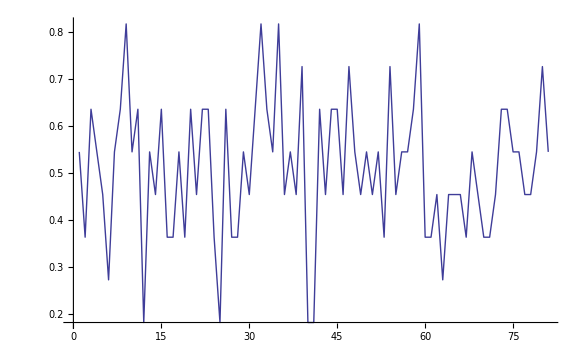

```mathematica
ListPlot[hitValues,Joined->True]
```

```mathematica
ParallelTable[{svmRun[SP500,2200,80,10,14,1,j,k],j,k},{j,25,75,25},{k,25,100,25}]
```

{{{0.909091,25,25},{0.909091,25,40},{0.909091,25,55},{0.909091,25,70},{0.909091,25,85},{0.909091,25,100}},{{0.909091,30,25},{0.909091,30,40},{0.909091,30,55},{0.909091,30,70},{0.909091,30,85},{0.909091,30,100}},{{0.909091,35,25},{0.909091,35,40},{0.909091,35,55},{0.909091,35,70},{0.909091,35,85},{0.909091,35,100}},{{0.909091,40,25},{0.909091,40,40},{0.909091,40,55},{0.909091,40,70},{0.909091,40,85},{0.909091,40,100}},{{0.909091,45,25},{0.909091,45,40},{0.909091,45,55},{0.909091,45,70},{0.909091,45,85},{0.909091,45,100}},{{0.909091,50,25},{0.909091,50,40},{0.909091,50,55},{0.909091,50,70},{0.909091,50,85},{0.909091,50,100}}}

```mathematica
.55*.55
```

0.3025

```mathematica
svmLongGDSearch[SP500,2200,30,10,14,1]
```

5 10 trading day periods.

{{{{0.545455,0,25,25},{0.454545,0,25,50},{0.454545,0,25,75},{0.363636,0,25,100}},{{0.545455,0,50,25},{0.454545,0,50,50},{0.272727,0,50,75},{0.272727,0,50,100}},{{0.454545,0,75,25},{0.363636,0,75,50},{0.272727,0,75,75},{0.272727,0,75,100}}},{{{0.454545,1,25,25},{0.454545,1,25,50},{0.454545,1,25,75},{0.454545,1,25,100}},{{0.363636,1,50,25},{0.454545,1,50,50},{0.454545,1,50,75},{0.545455,1,50,100}},{{0.363636,1,75,25},{0.454545,1,75,50},{0.545455,1,75,75},{0.545455,1,75,100}}},{{{0.727273,2,25,25},{0.727273,2,25,50},{0.727273,2,25,75},{0.636364,2,25,100}},{{0.727273,2,50,25},{0.727273,2,50,50},{0.727273,2,50,75},{0.727273,2,50,100}},{{0.727273,2,75,25},{0.727273,2,75,50},{0.727273,2,75,75},{0.727273,2,75,100}}},{{{0.454545,3,25,25},{0.454545,3,25,50},{0.454545,3,25,75},{0.363636,3,25,100}},{{0.454545,3,50,25},{0.363636,3,50,50},{0.363636,3,50,75},{0.363636,3,50,100}},{{0.363636,3,75,25},{0.363636,3,75,50},{0.363636,3,75,75},{0.363636,3,75,100}}},{{{0.727273,4,25,25},{0.636364,4,25,50},{0.727273,4,25,75},{0.727273,4,25,100}},{{0.636364,4,50,25},{0.727273,4,50,50},{0.727273,4,50,75},{0.818182,4,50,100}},{{0.636364,4,75,25},{0.727273,4,75,50},{0.727273,4,75,75},{0.818182,4,75,100}}},{{{0.727273,5,25,25},{0.727273,5,25,50},{0.727273,5,25,75},{0.727273,5,25,100}},{{0.727273,5,50,25},{0.727273,5,50,50},{0.727273,5,50,75},{0.727273,5,50,100}},{{0.727273,5,75,25},{0.727273,5,75,50},{0.727273,5,75,75},{0.727273,5,75,100}}}}

```mathematica
list={{{{0.5454545454545454,0,25,25},{0.45454545454545453,0,25,50},{0.45454545454545453,0,25,75},{0.36363636363636365,0,25,100}},{{0.5454545454545454,0,50,25},{0.45454545454545453,0,50,50},{0.2727272727272727,0,50,75},{0.2727272727272727,0,50,100}},{{0.45454545454545453,0,75,25},{0.36363636363636365,0,75,50},{0.2727272727272727,0,75,75},{0.2727272727272727,0,75,100}}},{{{0.45454545454545453,1,25,25},{0.45454545454545453,1,25,50},{0.45454545454545453,1,25,75},{0.45454545454545453,1,25,100}},{{0.36363636363636365,1,50,25},{0.45454545454545453,1,50,50},{0.45454545454545453,1,50,75},{0.5454545454545454,1,50,100}},{{0.36363636363636365,1,75,25},{0.45454545454545453,1,75,50},{0.5454545454545454,1,75,75},{0.5454545454545454,1,75,100}}},{{{0.7272727272727273,2,25,25},{0.7272727272727273,2,25,50},{0.7272727272727273,2,25,75},{0.6363636363636364,2,25,100}},{{0.7272727272727273,2,50,25},{0.7272727272727273,2,50,50},{0.7272727272727273,2,50,75},{0.7272727272727273,2,50,100}},{{0.7272727272727273,2,75,25},{0.7272727272727273,2,75,50},{0.7272727272727273,2,75,75},{0.7272727272727273,2,75,100}}},{{{0.45454545454545453,3,25,25},{0.45454545454545453,3,25,50},{0.45454545454545453,3,25,75},{0.36363636363636365,3,25,100}},{{0.45454545454545453,3,50,25},{0.36363636363636365,3,50,50},{0.36363636363636365,3,50,75},{0.36363636363636365,3,50,100}},{{0.36363636363636365,3,75,25},{0.36363636363636365,3,75,50},{0.36363636363636365,3,75,75},{0.36363636363636365,3,75,100}}},{{{0.7272727272727273,4,25,25},{0.6363636363636364,4,25,50},{0.7272727272727273,4,25,75},{0.7272727272727273,4,25,100}},{{0.6363636363636364,4,50,25},{0.7272727272727273,4,50,50},{0.7272727272727273,4,50,75},{0.8181818181818182,4,50,100}},{{0.6363636363636364,4,75,25},{0.7272727272727273,4,75,50},{0.7272727272727273,4,75,75},{0.8181818181818182,4,75,100}}},{{{0.7272727272727273,5,25,25},{0.7272727272727273,5,25,50},{0.7272727272727273,5,25,75},{0.7272727272727273,5,25,100}},{{0.7272727272727273,5,50,25},{0.7272727272727273,5,50,50},{0.7272727272727273,5,50,75},{0.7272727272727273,5,50,100}},{{0.7272727272727273,5,75,25},{0.7272727272727273,5,75,50},{0.7272727272727273,5,75,75},{0.7272727272727273,5,75,100}}}};
```

```mathematica
ParallelTable[Mean[list[[All,i,j,1]]],{i,1,3},{j,1,4}]
```

{{0.606061,0.575758,0.590909,0.545455},{0.575758,0.575758,0.545455,0.575758},{0.545455,0.560606,0.560606,0.575758}}

```mathematica
Mean[list[[All,1,1,1]]]
```

```mathematica
list[[All,1,1]]
```

{{0.545455,0,25,25},{0.454545,1,25,25},{0.727273,2,25,25},{0.454545,3,25,25},{0.727273,4,25,25},{0.727273,5,25,25}}

```mathematica
BubbleChart[newTest]
```

-Graphics-